```mathematica
Needs["MaTeX`"];
SetDirectory[NotebookDirectory[]]
```

/Users/mcmcclur/Documents/html/classes/Spring2020CalcIII/online_presentations/04.14.3DCoordinates/images

```mathematica
pt = {x,y,z}={1,Sqrt[3],2};
Graphics3D[{
{Black,Arrow[Tube[{{-2,0,0},{2,0,0}}]],
Arrow[Tube[{{0,-2,0},{0,2,0}}]],
Arrow[Tube[{{0,0,-1},{0,0,3}}]]},
PointSize[Large],Point[pt],
{Dashed,Arrowheads[Medium],Arrow[{{0,0,0},{x,y,0}}],
Line[{{x,y,0},{x,y,z}}]},
{Line@Table[0.6{Cos[t],Sin[t],0},{t,0,Pi/3,Pi/60}]},
Text[MaTeX["\\theta", FontSize-> 16],0.7{Cos[Pi/6],Sin[Pi/6],0}],
Text[MaTeX["r", FontSize-> 16],1.3{Cos[0.2+Pi/3],Sin[0.2+Pi/3],0}],
Text[MaTeX["z", FontSize-> 16],1.8{Cos[Pi/3],Sin[Pi/3],0.7}],
Text[MaTeX["(r,\\theta,z)", FontSize-> 16],2{Cos[Pi/3],Sin[Pi/3],1.1}]
},PlotRange -> {{-2,2},{-2,2},{-1,3}}, Boxed -> False, ImageSize -> 700]
```

-Graphics3D-

```mathematica
φ=Pi/6;
θ=Pi/3;
pt = {x,y,z} = {Sin[φ]Cos[θ],Sin[φ]Sin[θ],Cos[φ]};
r = 1.4;
Graphics3D[{
{Black,
Arrow[Tube[{{-0.9r,0,0},{r,0,0}}]],
Arrow[Tube[{{0,-0.9r,0},{0,r,0}}]],
Arrow[Tube[{{0,0,-0.9r},{0,0,r}}]]},
{Opacity[0.1],Sphere[{0,0,0},1]},
{PointSize[Large],Point[pt]},
{Arrow[{{0,0,0},pt}]},
{Dashed,Line[{{0,0,0},{x,y,0},{x,y,z}}]},
Line[Table[0.25{Cos[t],Sin[t],0},{t,0,θ,θ/50}]],
Line[Table[0.25{Sin[p]Cos[θ],Sin[p]Sin[θ],Cos[p]},{p,0,φ,φ/50}]],
Text[MaTeX["\\theta", FontSize->16],0.34{Cos[θ/3],Sin[θ/3],0}],
Text[MaTeX["\\varphi", FontSize->16],0.34{Sin[φ/2]Cos[θ],Sin[φ/2]Sin[θ],Cos[φ/2]}],
Text[MaTeX["\\rho", FontSize->16],0.5{Sin[φ+0.07]Cos[θ],Sin[φ+0.07]Sin[θ],Cos[φ+0.07]}]
}, Boxed->False, ImageSize->700, ViewPoint->{2.78,-1.166,1.5329}]
```

-Graphics3D-

```mathematica
φ=Pi/6;
θ=Pi/3;
pt = {x,y,z} = {Sin[φ]Cos[θ],Sin[φ]Sin[θ],Cos[φ]};
r = 1.4;
Graphics3D[{
{Black,
Arrow[Tube[{{-0.9r,0,0},{r,0,0}}]],
Arrow[Tube[{{0,-0.9r,0},{0,r,0}}]],
Arrow[Tube[{{0,0,-0.9r},{0,0,r}}]]},
{Opacity[0.1],Sphere[{0,0,0},1]},
{PointSize[Large],Point[pt]},
{Arrow[{{0,0,0},pt}]},
{Dashed,Line[{{0,0,0},{x,y,0},{x,y,z}}]},
Line[Table[0.25{Cos[t],Sin[t],0},{t,0,θ,θ/50}]],
Line[Table[0.25{Sin[p]Cos[θ],Sin[p]Sin[θ],Cos[p]},{p,0,φ,φ/50}]],
{Opacity[0.4],Polygon[2{{x,y,z},{x,y,0},{-x,-y,0},{-x,-y,z}}]},
Line[Table[{Sin[p]Cos[θ],Sin[p]Sin[θ],Cos[p]},{p,-Pi/2,Pi/2,Pi/50}]],
Text[MaTeX["\\theta", FontSize->16],0.34{Cos[θ/3],Sin[θ/3],0}],
Text[MaTeX["\\varphi", FontSize->16],0.34{Sin[φ/2]Cos[θ],Sin[φ/2]Sin[θ],Cos[φ/2]}],
Text[MaTeX["\\rho", FontSize->16],0.5{Sin[φ+0.07]Cos[θ],Sin[φ+0.07]Sin[θ],Cos[φ+0.07]}]
}, Boxed->False, ImageSize->700, ViewPoint->{2.78,-1.166,1.5329},
PlotRange->r]
```

-Graphics3D-

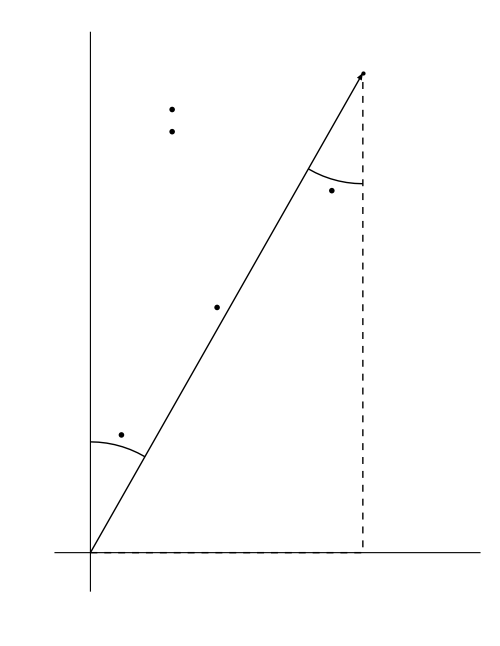

```mathematica
φ=Pi/6;
θ=Pi/3;
{x,y,z} = {Sin[φ]Cos[θ],Sin[φ]Sin[θ],Cos[φ]};
r = Sqrt[x^2+y^2];
Graphics[{
Arrow[{{0,0},{r,z}}],
PointSize[Large],Point[{r,z}],
Circle[{0,0},0.2,{Pi/2-φ,Pi/2}],
Circle[{r,z},0.2,{3Pi/2-φ,3Pi/2}],
{Dashed,Line[{{0,0},{r,0},{r,z}}]},
Text[MaTeX["\\varphi", FontSize->20],0.22{Sin[φ/2],Cos[φ/2]}],
Text[MaTeX["\\varphi", FontSize->20],{r,z}-0.22{Sin[φ/2],Cos[φ/2]}],
Text[MaTeX["\\rho", FontSize->20],0.5{Sin[φ-0.04],Cos[φ-0.04]}],
Text[MaTeX["r=\\rho\\sin(\\varphi)", FontSize->24], {0.15,0.8}],
Text[MaTeX["z=\\rho\\cos(\\varphi)", FontSize->24], {0.15,0.76}]
}, Axes->True, AxesOrigin->{0,0}, PlotRange->{{-0.05,0.7},{-0.05,0.92}},
Ticks -> {{{r,MaTeX["r", FontSize->20]}},{{z,MaTeX["z",FontSize->20]}}},
ImageSize->500]
```

```mathematica
Export["tri.png",%]
```

tri.png

```mathematica
rgb= RGBColor[0.37,0.51,.71];
rgb = RGBColor[0.880722,0.611041,0.142051];
topBot = ParametricPlot3D[{{r*Cos[t],r*Sin[t],0},{r*Cos[t],r*Sin[t],2}},{t,0,2Pi/3},{r,1,3},
PlotStyle -> rgb];
sides = ParametricPlot3D[{{r,0,z},{r*Cos[2Pi/3],r*Sin[2Pi/3],z}},{z,0,2},{r,1,3},
PlotStyle -> rgb];
inOut = ParametricPlot3D[{{Cos[t],Sin[t],z},{3*Cos[t],3*Sin[t],z}},{z,0,2},{t,0,2Pi/3},
PlotStyle -> rgb];
Show[{topBot,sides, inOut, 
Graphics3D[{Black,
Arrow[Tube[{{-1,0,0},{4,0,0}}]],
Arrow[Tube[{{0,-1,0},{0,4,0}}]],
Arrow[Tube[{{0,0,-1},{0,0,3}}]],
{Dashed,Line[{{1,0,2},{0,0,2},{Cos[2Pi/3],Sin[2Pi/3],2}}],
Line[{{0,0,0},{Cos[2Pi/3],Sin[2Pi/3],0}}]},
Line@Table[0.5{Cos[t],Sin[t],0},{t,0,2Pi/3,Pi/60}],
Text[MaTeX["\\beta", FontSize->16],{0.24,0.32,0}],
Text[MaTeX["a", FontSize->16],{1,-0.2,0}],
Text[MaTeX["b", FontSize->16],{3,-0.2,0}],
Text[MaTeX["d", FontSize->16],{-0.1,-0.1,2}]}
]}, Axes -> False, Boxed ->False, ImageSize-> 700]
```

-Graphics3D-

```mathematica
Clear[x,y,z,r,θ,t]
ParametricPlot3D[{r Cos[t],r Sin[t],4-r^2},{r,0,2},{t,0,2Pi},
BoxRatios->Automatic, ImageSize->700, Mesh->Full, PlotPoints -> 20,
MaxRecursion->5]
```

-Graphics3D-

```mathematica
pt = {x,y,z}={1,Sqrt[3],2};
Graphics3D[{
{Black,Tube[{{-2,0,0},{0,0,0}},0.015],Arrow[Tube[{{x,0,0},{2,0,0}}]],
Arrow[Tube[{{0,-2,0},{0,2,0}}]],
Arrow[Tube[{{0,0,-1},{0,0,3}}]]},
PointSize[Large],Point[pt],
{Dashed,Arrowheads[Medium],Arrow[{{0,0,0},{x,y,0}}],
Line[{{x,y,0},{x,y,z}}], Line[{{0,0,0},{x,0,0},{x,y,0}}]},
{Line@Table[0.6{Cos[t],Sin[t],0},{t,0,Pi/3,Pi/60}]},
Text[MaTeX["\\theta", FontSize-> 16],0.7{Cos[Pi/6],Sin[Pi/6],0}],
Text[MaTeX["r", FontSize-> 16],1.3{Cos[0.2+Pi/3],Sin[0.2+Pi/3],0}],
Text[MaTeX["z", FontSize-> 16],1.8{Cos[Pi/3],Sin[Pi/3],0.7}],
Text[MaTeX["(r,\\theta,z)", FontSize-> 16],2{Cos[Pi/3],Sin[Pi/3],1.1}],
Text[MaTeX["x", FontSize-> 16],{1/2,-0.2,0}],
Text[MaTeX["y", FontSize-> 16],{1.1,Sqrt[3]/2,0}]
},PlotRange -> {{-2,2},{-2,2},{-1,3}}, Boxed -> False, ImageSize->700]
```

-Graphics3D-

```mathematica
rgb= Lighter[RGBColor[0.37,0.51,.71], 0.7];
out = ParametricPlot3D[{
0.3{Sin[phi]Cos[theta],Sin[phi]Sin[theta],Cos[phi]},
{Sin[phi]Cos[theta],Sin[phi]Sin[theta],Cos[phi]}
},
{phi,0,Pi/2},{theta,0,Pi/2},PlotStyle -> rgb];
sides = ParametricPlot3D[{
{rho*Sin[phi]Cos[0],rho*Sin[phi]Sin[0],rho*Cos[phi]},
{rho*Sin[phi]Cos[Pi/2],rho*Sin[phi]Sin[Pi/2],rho*Cos[phi]}
},
{phi,0,Pi/2},{rho,0,1},PlotStyle -> rgb];
Show[{Graphics3D[{Black,
Arrow[Tube[{{-0.1,0,0},{1.4,0,0}}]],
Arrow[Tube[{{0,-0.1,0},{0,1.6,0}}]],
Arrow[Tube[{{0,0,-0.1},{0,0,1.4}}]]}],out,sides}, ImageSize -> 700,
Boxed -> False]
```

-Graphics3D-